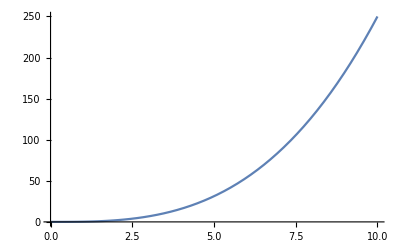

```mathematica
Module[{h,sol,h1},
h=0.5*g[x];
sol=NDSolve[{
f'[x]==x^2+g[x]+h,
g'[x]==x,
f[0]==2,
g[0]==0},{f,g},{x,0,10}];
h1[x_]=Integrate[h/.sol,x];
Plot[h1[x],{x,0,10}]
]
```

```mathematica
{InterpolatingFunction[{{0., 10.}}, <>][x]}
```

```mathematica
Plot[Integrate[x^2,x],{x,0,2}]
```

Integrate::ilim: Invalid integration variable or limit(s) in 0.0000408571.

Integrate::ilim: Invalid integration variable or limit(s) in 0.0408572.

Integrate::ilim: Invalid integration variable or limit(s) in 0.0816735.

General::stop: Further output of Integrate :: ilim will be suppressed during this calculation.

-Graphics-

x^3/3

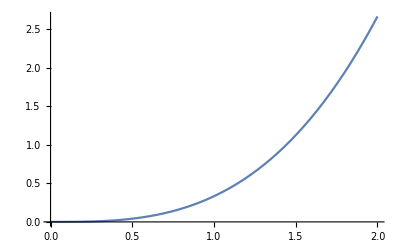

```mathematica
f[x_]=Integrate[x^2,x]
Plot[f[x],{x,0,2}]
```